# 共端复电流分配

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## 模型、输入与适用范围

Zi+e=V1; 1ᵀi=It

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

修改股数或回流几何；检查复电流及输入功率与损耗。

## 推导与结果解释

股线沿途绝缘，仅端部并联。二维 Az 弱形式把各导体区域与未知轴向电势梯度耦合，并用受控同轴铜回流闭合输运问题。

线性模型形成 Az 与源束/回流电势梯度的块系统。施加 ΣIi=20 A RMS、Ireturn=−20 A；各股共享源束电势梯度，复电流 Ii 由求得的电流密度积分得到。

分别积分束线及回流焦耳损耗，与输入有功功率比较。纯输运工况可定义 Rac,bundle=Pbundle/|It|.b2。七股为方法演示，铜面积不满足 Q2。

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## 可编辑参数

```mathematica
parameters=<|"strands"->7,"diameter_m"->0.0001,"mesh_factor"->0.7,"return_factor"->2.,"outer_factor"->1.5,"minimum_segments"->24|>;parameters
```

<|strands -> 7, diameter_m -> 0.0001, mesh_factor -> 0.7, 
 
>   return_factor -> 2., outer_factor -> 1.5, minimum_segments -> 24|>

## 独立进程执行与结果

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"coax",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_coax_20261014005546_0758f2d0, 
 
>   source_model -> 2D_linear_triangle_Az_common_voltage_coax_FEM, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

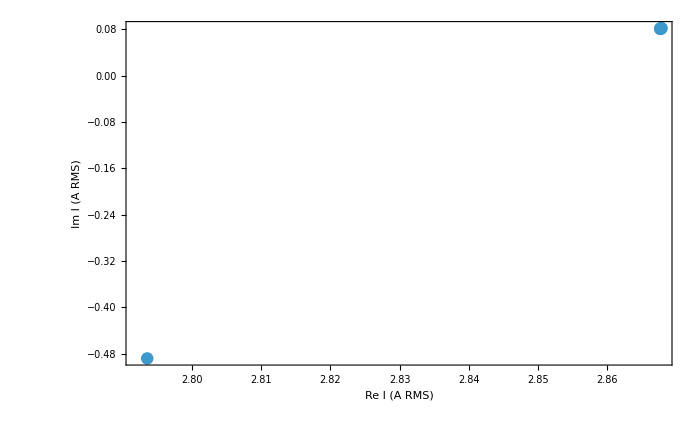

```mathematica
LitzNotebook`DisplayResearch[research]
```

## 验收与接续

核对结果中的 checks、execution_status 和 physical_acceptance_status。完整收敛与结构研究按路线 README 继续。

Sources: P01, P02; references/library.bib and references/sources.json

## 历史证据

data/evidence/v1.0.0-rc.1/; litz-research data fetch common-terminal